### function(s)

```mathematica
Needs["PlotLegends`"];
SetDirectory["/home/moosmann/mathematica/multileptons"];

mu=105.658369 10^6 ; (*muon mass*)

(*Substitute x1 by x2 using the expression for the invariant mass*)
Block[{solx1m},
{solx1p,solx1m}=Evaluate[x1/.Simplify[Solve[X^2==2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]]];
solx1p];

(*condition for x1=f(x2,X,cos(θ)) to be real and positiv*)
solx1sqrtcon=Boole[(-4 X^2+X^4+4 (-1+cos^2) x2^2)>0];

(*Jacobian determinant jx1Xp=(d/dx1 X^2)^-1 with x1 substituted by solx1p, where X^2 is given by the dimless invariant mass and dx1=2*X*jx1Xp*dX *)
jx1Xp=Simplify[1/D[2(1+Sqrt[1+x1^2]Sqrt[1+x2^2]-x1 x2 cos),x1]/.x1->solx1p];

(*relative angle condition*)
Block[{n},
n[cos_,p_]:={Sqrt[1-cos^2]Cos[2π p],Sqrt[1-cos^2]Sin[2π p],cos};
cos12=n[cos1,p1]. n[cos2,p2];
angcon=Boole[Evaluate[cos12]>cosmin];
]

(*transversal impuls cut-off*)
ptcut=Boole[(1-cos1^2)x1^2>((ptmin  10^9)/mu)^2]*Boole[(1-cos2^2)x2^2>((ptmin  10^9)/mu)^2]/.{x1->solx1p};

(* function that gives the data to plot {X,#f/ΔX} *)
Remove[plotdata];
plotdata[yy_,CosMin_,acgoal_,prgoal_,partlist_List,Xmax_:10,points_:40,pt_]:=
Block[{dX=(Xmax-2)/points,y=yy,cosmin=CosMin,ptmin=pt,cos=cos12,plot,int,time},

int= Evaluate[
ptcut angcon solx1sqrtcon jx1Xp
 solx1p^3/Sqrt[solx1p^2+1] 1/(Exp[1/(11.24/(2π)y) Sqrt[1+solx1p^2]]+1) 
x2^3/Sqrt[x2^2+1] 1/(Exp[1/(11.24/(2π)y) Sqrt[1+x2^2]]+1)
];


Table[{X,
2X (*change from dx1->dX*)(2π)^2(*change from ϕ->2πp*)(1/(8 π^3))^2(*original prefactor*)NIntegrate[
int,
{x2,0,Sqrt[X^2(X^2-1)/4]},{cos1,-1,1},{cos2,-1,1},{p1,0,1},{p2,0,1},
Method->{"AdaptiveQuasiMonteCarlo","Partitioning"->partlist},
AccuracyGoal->acgoal,
PrecisionGoal->prgoal
]},{X,2,Xmax,dX}
]

];
```

### data

#### y = 1, cos = -1

```mathematica
Timing[pdaty1cosMinus1ptcut0=plotdata[1,-1,1,1,{2,2,2,2,2},20,50,0];]
```

{76.2768,Null}

```mathematica
Timing[pdaty1cosMinus1ptcut1=plotdata[1,-1,2,2,{4,3,3,3,3},40,60,1];]
```

{944.371,Null}

```mathematica
Timing[pdaty1cosMinus1ptcut3=plotdata[1,-1,1,1,{2,2,2,1,1},20,50,3];]
```

{21.1733,Null}

```mathematica
Timing[pdaty1cosMinus1ptcut5=plotdata[1,-1,1,1,{2,2,2,1,1},20,50,5];]
```

{22.2094,Null}

#### y = 1, cos = .8

```mathematica
Timing[pdaty1cosCDFptcut0=plotdata[1,.8,1,1,{2,2,2,2,2},10,50,0];]
```

{77.3008,Null}

```mathematica
Timing[pdaty1cosCDFptcut1=plotdata[1,.8,2,2,{4,3,3,3,3},15,45,1];]
```

{705.328,Null}

```mathematica
Timing[pdaty1cosCDFptcut3=plotdata[1,.8,1,1,{2,2,2,1,1},20,50,3];]
```

{21.9614,Null}

```mathematica
Timing[pdaty1cosCDFptcut5=plotdata[1,.8,1,1,{2,2,2,1,1},20,50,5];]
```

{22.0494,Null}

#### y = .5, cos = -1

```mathematica
Timing[pdatyHalfcosMinus1ptcut0=plotdata[.5,-1,1,1,{1,1,1,1,1},20,100,0];]
```

{8.51653,Null}

```mathematica
Timing[pdatyHalfcosMinus1ptcut1=plotdata[.5,-1,1,1,{2,2,2,1,1},40,50,1];]
```

{21.4333,Null}

```mathematica
Timing[pdatyHalfcosMinus1ptcut3=plotdata[.5,-1,1,1,{2,2,2,1,1},20,50,3];]
```

{22.1374,Null}

```mathematica
Timing[pdatyHalfcosMinus1ptcut5=plotdata[.5,-1,1,1,{2,2,2,1,1},20,50,5];]
```

{21.3573,Null}

#### y = .5, cos = .8

```mathematica
Timing[pdatyHalfcosCDFptcut0=plotdata[.5,.8,1,1,{2,2,2,1,1},10,100,0];]
```

{27.1697,Null}

```mathematica
Timing[pdatyHalfcosCDFptcut1=plotdata[.5,.8,1,1,{2,2,2,1,1},15,45,1];]
```

{19.1892,Null}

```mathematica
Timing[pdatyHalfcosCDFptcut3=plotdata[.5,.8,1,1,{2,2,2,1,1},20,50,3];]
```

{20.7933,Null}

```mathematica
Timing[pdatyHalfcosCDFptcut5=plotdata[.5,.8,1,1,{2,2,2,1,1},20,50,5];]
```

{21.6574,Null}

### plots

#### single plot

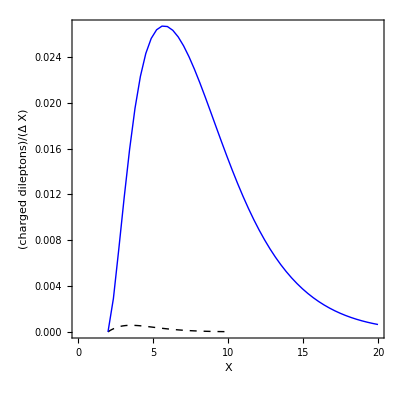

```mathematica
ShowLegend[
ListPlot[{pdatyHalfcosMinus1ptcut0,pdaty1cosMinus1ptcut0},
PlotRange->Full,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Black,Dashed},{Blue}},
Frame->True,FrameLabel->{"X","(charged dileptons)/(Δ X)"},FrameTicks->{{All,None},{All,None}},
AxesOrigin->{0,0},AspectRatio->1]
,{{{Graphics[{Blue,Line[{{0,0},{1.5,0}}]}],"y = 1"},{Graphics[{Black,Dashed,Line[{{0,0},{1.5,0}}]}],"y = .5"}},LegendPosition->{1.1,-.4}}
]
```

#### test

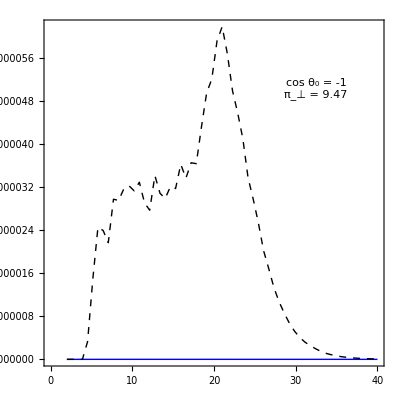

```mathematica
ListPlot[{pdatyHalfcosMinus1ptcut1,pdaty1cosMinus1ptcut1},
PlotRange->Full,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]]
```

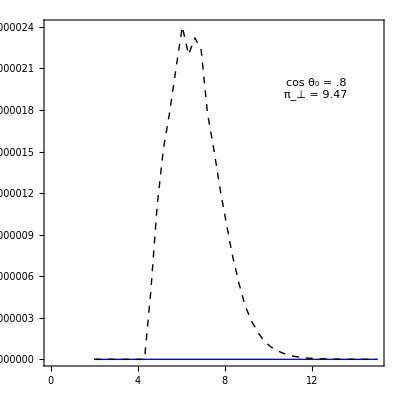

```mathematica
ListPlot[{pdatyHalfcosCDFptcut1,pdaty1cosCDFptcut1},
PlotRange->Full,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]]
```

#### multi plots

```mathematica
Block[{plot,lamb,l},

lamb[list_List]:=Block[{},
l=Length@list;
Table[{1,4}list[[i]],{i,1,l}]];

plot=ShowLegend[
GraphicsGrid[{{
ListPlot[{lamb@pdatyHalfcosMinus1ptcut0,lamb@pdaty1cosMinus1ptcut0},
PlotRange->Full,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 0"}}],10]],Scaled[{.8,.8}]]],
ListPlot[{lamb@pdatyHalfcosCDFptcut0,lamb@pdaty1cosCDFptcut0},
PlotRange->Full,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 0"}}],10]],Scaled[{.8,.8}]]]
},{
ListPlot[{lamb@pdatyHalfcosMinus1ptcut1,lamb@pdaty1cosMinus1ptcut1},
PlotRange->Full,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = -1"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]],
ListPlot[{lamb@pdatyHalfcosCDFptcut1,lamb@pdaty1cosCDFptcut1},
PlotRange->Full,PerformanceGoal->"Quality",Joined->True,PlotStyle->{{Blue},{Black,Dashed}},Frame->True,FrameTicks->{{All,None},{All,None}},AxesOrigin->{0,0},AspectRatio->1,
Epilog->Inset[Framed[Style[TableForm[{{"cos θ_0 = .8"},{"π_⊥ = 9.47"}}],10]],Scaled[{.8,.8}]]]
}},ImageSize->Large]
,{{{Graphics[{Black,Dashed,Line[{{0,0},{1.5,0}}]}],"y = 1"},{Graphics[{Blue,Line[{{0,0},{1.5,0}}]}],"y = .5"}},LegendPosition->{1.1,-.250},LegendSize->{.3,.5}}
];

Export["dilepton-spectrum-new-times16.eps",Evaluate@Labeled[plot,X,{Bottom,Left}],"eps"];

plot
]
```

-Graphics-

#### diverse plots

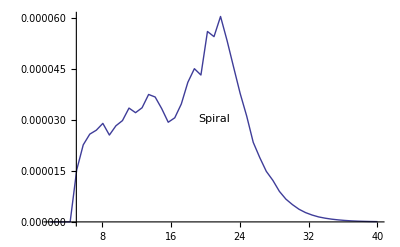

```mathematica
ListPlot[pdaty1cosMinus1ptcut1,PlotRange->Full,Joined->True,
Epilog->Inset[Framed[Style["Spiral",10]],Scaled[{.8,.8}]]]
```

```mathematica
Timing[pdaty1cosMinus1ptcut1=plotdata[1,-1,2,2,{3,3,3,3,3},40,50,1];]
```

{612.25,Null}

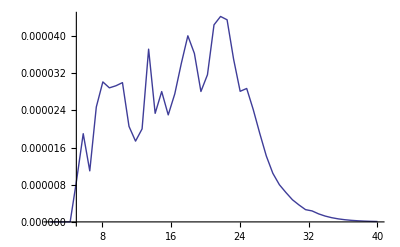

```mathematica
ListPlot[plotdata[1,-1,2,2,{2,2,2,2,2},40,50,1],PlotRange->Full,Joined->True]
```

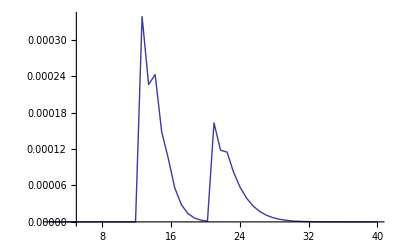

```mathematica
ListPlot[plotdata[1,-1,1,1,{1,1,1,1,1},40,50,1],PlotRange->Full,Joined->True]
```

### prefactor stuff

```mathematica
(* energy per unit time and surface / m^4 *)
JTH[y_,x0_]:=1/(4 π^2)*NIntegrate[x^3/(Exp[2π/(11.24 y)x]+1)+2 x^3/(Exp[2π/(11.24y)Sqrt[1+x^2]]+1),{x,0,x0},MaxRecursion->100];
(* prefactor*m^3 to multiplied with fermion spectrum to yield the total number of fermions *)
prefactor[y_,d_:1,ECOM_:1 10^12]:=1/mu 4π  (d ECOM/mu)/(4π JTH[y,100]);
```

```mathematica
prefactor[1]
```

2204.06

```mathematica
prefactor[.5]
```

38230.

#### testing

```mathematica
TableForm@Table[JTH[y,10^x],{y,{.1,.5,1}},{x,-1,6}]
```

2.51742×10^-7 | 0.000128627 | 0.000167159 | 0.000167159 | 0.000167159 | 0.000167159 | 0.000167159 | 0.000167159
6.13652×10^-7 | 0.00427993 | 0.246355 | 0.247566 | 0.247566 | 0.247566 | 0.247566 | 0.247566
7.69736×10^-7 | 0.00661962 | 3.41345 | 4.29411 | 4.29411 | 4.29411 | 4.29411 | 4.29411

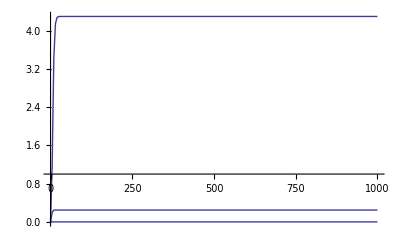

```mathematica
Plot[Table[JTH[y,x0],{y,{.1,.5,1}}],{x0,0,1000},PerformanceGoal->"Speed",PlotRange->Full,AxesOrigin->{0,1}]
```